```mathematica
f[x1_,x2_]=-8x2+4 x1^2+2 x2^2-4x1 x2; (*функція*)
g[x1_,x2_]={x1^2+x2^2-5}; (*область пошуку*)
center={0,0}; (*центр заданої області пошуку*)
r=5^(1/2); (*радіус кола*)
ϵ=10.^-3;
X0={2.,1.}; 
(*початкова точка*)
α=0.1; (*крок*)
(*точне вирішення задачі мінімізації*)
point=NMinimize[{f[x1,x2],g[x1,x2][[1]]≤0},{x1,x2}][[2,;;,2]]
```

{0.863619,2.06256}

Таблиця результатів:
k | X^(k) | X^(k)∈G | f(X^(k))
1 | {2.,1.} | True | 2.
2 | {0.8,2.2} | False | -12.4
2 | {0.764161,2.10144} | False | -12.067
3 | {0.993409,2.36653} | False | -13.1876
3 | {0.865483,2.06178} | True | -12.1339
4 | {0.997809,2.38326} | False | -13.2359
4 | {0.863552,2.06259} | False | -12.1339
5 | {0.997746,2.38297} | False | -13.2351
5 | {0.863595,2.06257} | True | -12.1339

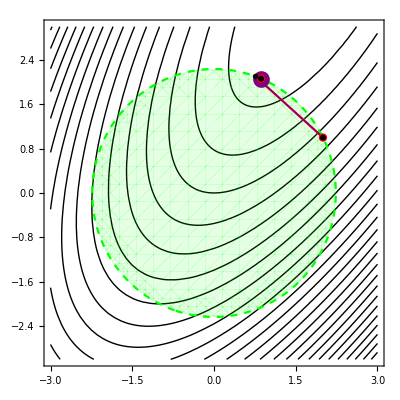

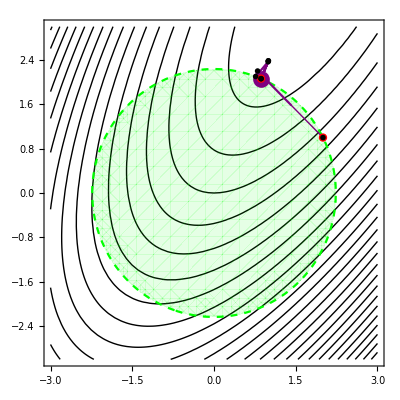

Час роботи методу: 0.012556 s
Нев'язка: 0.0000269984
Похибка: 4.34486×10^-9
Отримане значення: {0.863595,2.06257}
Значення функції: -12.1339

```mathematica
(* реалізація методу проекції градієнта *)
Gr[f_,X0_]:=Grad[f[x1,x2],{x1,x2}]/.Thread[{x1,x2}->X0]
t1=Now;
G=ImplicitRegion[g[x1,x2][[1]]≤0,{x1,x2}];
X={X0};
XX={X0};
(*масив результатів*)
res={{"k","X^(k)","X^(k)∈G","f(X^(k))"}};
tempX=X0;
If[tempX∈G,{
AppendTo[X,tempX];
AppendTo[res,{1,XX[[-1]],XX[[-1]]∈G,f[XX[[-1,1]],XX[[-1,2]]]}];

},{
tempX1=center+r/Norm[tempX-center](tempX-center);
AppendTo[X,tempX1];
AppendTo[XX,tempX1];
AppendTo[res,{1,tempX,tempX∈G,f[tempX[[1]],tempX[[2]]]}];
AppendTo[res,{1,tempX1,tempX1∈G,f[tempX1[[1]],tempX1[[2]]]}];
}];

Do[{
grad=Gr[f,X[[-1]]];
tempX=X[[-1]]-α grad/1;
AppendTo[XX,tempX];

If[tempX∈G,{
AppendTo[X,tempX];
AppendTo[res,{i,XX[[-1]],XX[[-1]]∈G,f[XX[[-1,1]],XX[[-1,2]]]}];

},{
tempX1=center+r/Norm[tempX-center](tempX-center);
AppendTo[X,tempX1];
AppendTo[XX,tempX1];
AppendTo[res,{i,tempX,tempX∈G,f[tempX[[1]],tempX[[2]]]}];
AppendTo[res,{i,tempX1,tempX1∈G,f[tempX1[[1]],tempX1[[2]]]}];
}];


If[Norm[X[[-1]]-X[[-2]]]≤ϵ,Break[]];
},{i,2,200}];

t2=Now;

Print["Таблиця результатів:\n",Grid[res]];


Print[Show[
ContourPlot[f[x1,x2],{x1,-3,3},{x2,-3,3},ContourShading->None,Contours->{Automatic,50}],

RegionPlot[g[x1,x2][[1]]≤0,{x1,-3,3},{x2,-3,3},PlotStyle->{Green,Opacity[0.1]},BoundaryStyle->{Dashed,Green}],

ListLinePlot[X,ColorFunction->Function[{x,y},Hue[y]]],

Graphics[{Purple,PointSize[0.03],Point[point],Line[X],Red,PointSize[0.015],Point[{X[[1]],X[[-1]]}],Black,PointSize[0.01],Point[X[[;;-2]]]}]

]];
Print[Show[
ContourPlot[f[x1,x2],{x1,-3,3},{x2,-3,3},ContourShading->None,Contours->{Automatic,50}],

RegionPlot[g[x1,x2][[1]]≤0,{x1,-3,3},{x2,-3,3},PlotStyle->{Green,Opacity[0.1]},BoundaryStyle->{Dashed,Green}],

ListLinePlot[XX,ColorFunction->Function[{x,y},Hue[y]]],

Graphics[{Purple,PointSize[0.03],Point[point],Line[XX],Red,PointSize[0.015],Point[{X[[1]],X[[-1]]}],Black,PointSize[0.01],Point[XX[[;;-2]]]}]

]];
Print["Час роботи методу: ",t=t2-t1, "\nНев'язка: ",Norm[point-X[[-1]]],"\nПохибка: ",Abs[f[point[[1]],point[[2]]]-f[X[[-1,1]],X[[-1,2]]]],"\nОтримане значення: ",X[[-1]],"\nЗначення функції: ",f[X[[-1,1]],X[[-1,2]]]];

Gr[f_,X0_]:=Grad[f[x1,x2],{x1,x2}]/.Thread[{x1,x2}->X0]
```